```mathematica
Clear[Evaluate[Context[]<>"*"]];
DSolve[{a'[t]==-k1*a[t],b'[t]==k1*a[t]-k2*b[t],c'[t]==k2*b[t]-k3*c[t],d'[t]==k3*c[t]-k4*d[t],e'[t]==k4*d[t]},{a[t],b[t],c[t],d[t],e[t]},t]
```

{{a[t]→ⅇ^(-k1 t) C[1],b[t]→-(ⅇ^(-k1 t-k2 t) (-ⅇ^(k1 t)+ⅇ^(k2 t)) k1 C[1])/(k1-k2)+ⅇ^(-k2 t) C[2],c[t]→(ⅇ^(-k1 t-k2 t-k3 t) k1 k2 (ⅇ^(k1 t+k2 t) k1-ⅇ^(k1 t+k3 t) k1-ⅇ^(k1 t+k2 t) k2+ⅇ^(k2 t+k3 t) k2+ⅇ^(k1 t+k3 t) k3-ⅇ^(k2 t+k3 t) k3) C[1])/((k1-k2) (k1-k3) (k2-k3))-(ⅇ^(-k2 t-k3 t) (-ⅇ^(k2 t)+ⅇ^(k3 t)) k2 C[2])/(k2-k3)+ⅇ^(-k3 t) C[3],d[t]→1/((-k1+k2) (k1-k3) (k2-k3) (k1-k4) (k2-k4) (k3-k4))ⅇ^(-k1 t-k2 t-k3 t-k4 t) k1 k2 k3 (-ⅇ^(k1 t+k2 t+k3 t) k1^2 k2+ⅇ^(k1 t+k2 t+k4 t) k1^2 k2+ⅇ^(k1 t+k2 t+k3 t) k1 k2^2-ⅇ^(k1 t+k2 t+k4 t) k1 k2^2+ⅇ^(k1 t+k2 t+k3 t) k1^2 k3-ⅇ^(k1 t+k3 t+k4 t) k1^2 k3-ⅇ^(k1 t+k2 t+k3 t) k2^2 k3+ⅇ^(k2 t+k3 t+k4 t) k2^2 k3-ⅇ^(k1 t+k2 t+k3 t) k1 k3^2+ⅇ^(k1 t+k3 t+k4 t) k1 k3^2+ⅇ^(k1 t+k2 t+k3 t) k2 k3^2-ⅇ^(k2 t+k3 t+k4 t) k2 k3^2-ⅇ^(k1 t+k2 t+k4 t) k1^2 k4+ⅇ^(k1 t+k3 t+k4 t) k1^2 k4+ⅇ^(k1 t+k2 t+k4 t) k2^2 k4-ⅇ^(k2 t+k3 t+k4 t) k2^2 k4-ⅇ^(k1 t+k3 t+k4 t) k3^2 k4+ⅇ^(k2 t+k3 t+k4 t) k3^2 k4+ⅇ^(k1 t+k2 t+k4 t) k1 k4^2-ⅇ^(k1 t+k3 t+k4 t) k1 k4^2-ⅇ^(k1 t+k2 t+k4 t) k2 k4^2+ⅇ^(k2 t+k3 t+k4 t) k2 k4^2+ⅇ^(k1 t+k3 t+k4 t) k3 k4^2-ⅇ^(k2 t+k3 t+k4 t) k3 k4^2) C[1]+(ⅇ^(-k2 t-k3 t-k4 t) k2 k3 (ⅇ^(k2 t+k3 t) k2-ⅇ^(k2 t+k4 t) k2-ⅇ^(k2 t+k3 t) k3+ⅇ^(k3 t+k4 t) k3+ⅇ^(k2 t+k4 t) k4-ⅇ^(k3 t+k4 t) k4) C[2])/((k2-k3) (k2-k4) (k3-k4))-(ⅇ^(-k3 t-k4 t) (-ⅇ^(k3 t)+ⅇ^(k4 t)) k3 C[3])/(k3-k4)+ⅇ^(-k4 t) C[4],e[t]→-1/((-k1+k2) (k1-k3) (k2-k3) (k1-k4) (k2-k4) (k3-k4))ⅇ^(-k1 t-k2 t-k3 t-k4 t) (-ⅇ^(k1 t+k2 t+k3 t) k1^3 k2^2 k3+ⅇ^(k1 t+k2 t+k3 t+k4 t) k1^3 k2^2 k3+ⅇ^(k1 t+k2 t+k3 t) k1^2 k2^3 k3-ⅇ^(k1 t+k2 t+k3 t+k4 t) k1^2 k2^3 k3+ⅇ^(k1 t+k2 t+k3 t) k1^3 k2 k3^2-ⅇ^(k1 t+k2 t+k3 t+k4 t) k1^3 k2 k3^2-ⅇ^(k1 t+k2 t+k3 t) k1 k2^3 k3^2+ⅇ^(k1 t+k2 t+k3 t+k4 t) k1 k2^3 k3^2-ⅇ^(k1 t+k2 t+k3 t) k1^2 k2 k3^3+ⅇ^(k1 t+k2 t+k3 t+k4 t) k1^2 k2 k3^3+ⅇ^(k1 t+k2 t+k3 t) k1 k2^2 k3^3-ⅇ^(k1 t+k2 t+k3 t+k4 t) k1 k2^2 k3^3+ⅇ^(k1 t+k2 t+k4 t) k1^3 k2^2 k4-ⅇ^(k1 t+k2 t+k3 t+k4 t) k1^3 k2^2 k4-ⅇ^(k1 t+k2 t+k4 t) k1^2 k2^3 k4+ⅇ^(k1 t+k2 t+k3 t+k4 t) k1^2 k2^3 k4-ⅇ^(k1 t+k3 t+k4 t) k1^3 k3^2 k4+ⅇ^(k1 t+k2 t+k3 t+k4 t) k1^3 k3^2 k4+ⅇ^(k2 t+k3 t+k4 t) k2^3 k3^2 k4-ⅇ^(k1 t+k2 t+k3 t+k4 t) k2^3 k3^2 k4+ⅇ^(k1 t+k3 t+k4 t) k1^2 k3^3 k4-ⅇ^(k1 t+k2 t+k3 t+k4 t) k1^2 k3^3 k4-ⅇ^(k2 t+k3 t+k4 t) k2^2 k3^3 k4+ⅇ^(k1 t+k2 t+k3 t+k4 t) k2^2 k3^3 k4-ⅇ^(k1 t+k2 t+k4 t) k1^3 k2 k4^2+ⅇ^(k1 t+k2 t+k3 t+k4 t) k1^3 k2 k4^2+ⅇ^(k1 t+k2 t+k4 t) k1 k2^3 k4^2-ⅇ^(k1 t+k2 t+k3 t+k4 t) k1 k2^3 k4^2+ⅇ^(k1 t+k3 t+k4 t) k1^3 k3 k4^2-ⅇ^(k1 t+k2 t+k3 t+k4 t) k1^3 k3 k4^2-ⅇ^(k2 t+k3 t+k4 t) k2^3 k3 k4^2+ⅇ^(k1 t+k2 t+k3 t+k4 t) k2^3 k3 k4^2-ⅇ^(k1 t+k3 t+k4 t) k1 k3^3 k4^2+ⅇ^(k1 t+k2 t+k3 t+k4 t) k1 k3^3 k4^2+ⅇ^(k2 t+k3 t+k4 t) k2 k3^3 k4^2-ⅇ^(k1 t+k2 t+k3 t+k4 t) k2 k3^3 k4^2+ⅇ^(k1 t+k2 t+k4 t) k1^2 k2 k4^3-ⅇ^(k1 t+k2 t+k3 t+k4 t) k1^2 k2 k4^3-ⅇ^(k1 t+k2 t+k4 t) k1 k2^2 k4^3+ⅇ^(k1 t+k2 t+k3 t+k4 t) k1 k2^2 k4^3-ⅇ^(k1 t+k3 t+k4 t) k1^2 k3 k4^3+ⅇ^(k1 t+k2 t+k3 t+k4 t) k1^2 k3 k4^3+ⅇ^(k2 t+k3 t+k4 t) k2^2 k3 k4^3-ⅇ^(k1 t+k2 t+k3 t+k4 t) k2^2 k3 k4^3+ⅇ^(k1 t+k3 t+k4 t) k1 k3^2 k4^3-ⅇ^(k1 t+k2 t+k3 t+k4 t) k1 k3^2 k4^3-ⅇ^(k2 t+k3 t+k4 t) k2 k3^2 k4^3+ⅇ^(k1 t+k2 t+k3 t+k4 t) k2 k3^2 k4^3) C[1]+(ⅇ^(-k2 t-k3 t-k4 t) (-ⅇ^(k2 t+k3 t) k2^2 k3+ⅇ^(k2 t+k3 t+k4 t) k2^2 k3+ⅇ^(k2 t+k3 t) k2 k3^2-ⅇ^(k2 t+k3 t+k4 t) k2 k3^2+ⅇ^(k2 t+k4 t) k2^2 k4-ⅇ^(k2 t+k3 t+k4 t) k2^2 k4-ⅇ^(k3 t+k4 t) k3^2 k4+ⅇ^(k2 t+k3 t+k4 t) k3^2 k4-ⅇ^(k2 t+k4 t) k2 k4^2+ⅇ^(k2 t+k3 t+k4 t) k2 k4^2+ⅇ^(k3 t+k4 t) k3 k4^2-ⅇ^(k2 t+k3 t+k4 t) k3 k4^2) C[2])/((k2-k3) (k2-k4) (k3-k4))+(ⅇ^(-k3 t-k4 t) (ⅇ^(k3 t) k3-ⅇ^(k3 t+k4 t) k3-ⅇ^(k4 t) k4+ⅇ^(k3 t+k4 t) k4) C[3])/(-k3+k4)+ⅇ^(-k4 t) (-1+ⅇ^(k4 t)) C[4]+C[5]}}

```mathematica
DSolve[{a'[t]==-kA*a[t],b'[t]==kA*a[t]-kB*b[t],c'[t]==kB*b[t]},{a[t],b[t],c[t]},t]
```

{{a[t]→ⅇ^(-kA t) C[1],b[t]→-(ⅇ^(-kA t-kB t) (-ⅇ^(kA t)+ⅇ^(kB t)) kA C[1])/(kA-kB)+ⅇ^(-kB t) C[2],c[t]→(ⅇ^(-kA t-kB t) (ⅇ^(kA t) kA-ⅇ^(kA t+kB t) kA-ⅇ^(kB t) kB+ⅇ^(kA t+kB t) kB) C[1])/(-kA+kB)+ⅇ^(-kB t) (-1+ⅇ^(kB t)) C[2]+C[3]}}

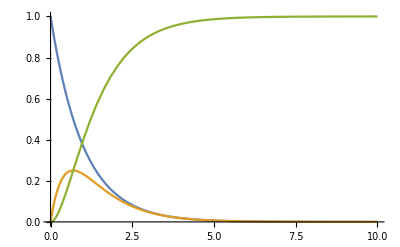

```mathematica
kA=1;kB=2;Plot[{ⅇ^(-kA t),-(ⅇ^(-kA t-kB t) (-ⅇ^(kA t)+ⅇ^(kB t)) kA)/(kA-kB),(ⅇ^(-kA t-kB t) (ⅇ^(kA t) kA-ⅇ^(kA t+kB t) kA-ⅇ^(kB t) kB+ⅇ^(kA t+kB t) kB))/(-kA+kB)},{t,0,10}]
```

```mathematica
D[-1/((-k1+k2) (k1-k3) (k2-k3) (k1-k4) (k2-k4) (k3-k4))ⅇ^(-k1 t-k2 t-k3 t-k4 t) (-ⅇ^(k1 t+k2 t+k3 t) k1^3 k2^2 k3+ⅇ^(k1 t+k2 t+k3 t+k4 t) k1^3 k2^2 k3+ⅇ^(k1 t+k2 t+k3 t) k1^2 k2^3 k3-ⅇ^(k1 t+k2 t+k3 t+k4 t) k1^2 k2^3 k3+ⅇ^(k1 t+k2 t+k3 t) k1^3 k2 k3^2-ⅇ^(k1 t+k2 t+k3 t+k4 t) k1^3 k2 k3^2-ⅇ^(k1 t+k2 t+k3 t) k1 k2^3 k3^2+ⅇ^(k1 t+k2 t+k3 t+k4 t) k1 k2^3 k3^2-ⅇ^(k1 t+k2 t+k3 t) k1^2 k2 k3^3+ⅇ^(k1 t+k2 t+k3 t+k4 t) k1^2 k2 k3^3+ⅇ^(k1 t+k2 t+k3 t) k1 k2^2 k3^3-ⅇ^(k1 t+k2 t+k3 t+k4 t) k1 k2^2 k3^3+ⅇ^(k1 t+k2 t+k4 t) k1^3 k2^2 k4-ⅇ^(k1 t+k2 t+k3 t+k4 t) k1^3 k2^2 k4-ⅇ^(k1 t+k2 t+k4 t) k1^2 k2^3 k4+ⅇ^(k1 t+k2 t+k3 t+k4 t) k1^2 k2^3 k4-ⅇ^(k1 t+k3 t+k4 t) k1^3 k3^2 k4+ⅇ^(k1 t+k2 t+k3 t+k4 t) k1^3 k3^2 k4+ⅇ^(k2 t+k3 t+k4 t) k2^3 k3^2 k4-ⅇ^(k1 t+k2 t+k3 t+k4 t) k2^3 k3^2 k4+ⅇ^(k1 t+k3 t+k4 t) k1^2 k3^3 k4-ⅇ^(k1 t+k2 t+k3 t+k4 t) k1^2 k3^3 k4-ⅇ^(k2 t+k3 t+k4 t) k2^2 k3^3 k4+ⅇ^(k1 t+k2 t+k3 t+k4 t) k2^2 k3^3 k4-ⅇ^(k1 t+k2 t+k4 t) k1^3 k2 k4^2+ⅇ^(k1 t+k2 t+k3 t+k4 t) k1^3 k2 k4^2+ⅇ^(k1 t+k2 t+k4 t) k1 k2^3 k4^2-ⅇ^(k1 t+k2 t+k3 t+k4 t) k1 k2^3 k4^2+ⅇ^(k1 t+k3 t+k4 t) k1^3 k3 k4^2-ⅇ^(k1 t+k2 t+k3 t+k4 t) k1^3 k3 k4^2-ⅇ^(k2 t+k3 t+k4 t) k2^3 k3 k4^2+ⅇ^(k1 t+k2 t+k3 t+k4 t) k2^3 k3 k4^2-ⅇ^(k1 t+k3 t+k4 t) k1 k3^3 k4^2+ⅇ^(k1 t+k2 t+k3 t+k4 t) k1 k3^3 k4^2+ⅇ^(k2 t+k3 t+k4 t) k2 k3^3 k4^2-ⅇ^(k1 t+k2 t+k3 t+k4 t) k2 k3^3 k4^2+ⅇ^(k1 t+k2 t+k4 t) k1^2 k2 k4^3-ⅇ^(k1 t+k2 t+k3 t+k4 t) k1^2 k2 k4^3-ⅇ^(k1 t+k2 t+k4 t) k1 k2^2 k4^3+ⅇ^(k1 t+k2 t+k3 t+k4 t) k1 k2^2 k4^3-ⅇ^(k1 t+k3 t+k4 t) k1^2 k3 k4^3+ⅇ^(k1 t+k2 t+k3 t+k4 t) k1^2 k3 k4^3+ⅇ^(k2 t+k3 t+k4 t) k2^2 k3 k4^3-ⅇ^(k1 t+k2 t+k3 t+k4 t) k2^2 k3 k4^3+ⅇ^(k1 t+k3 t+k4 t) k1 k3^2 k4^3-ⅇ^(k1 t+k2 t+k3 t+k4 t) k1 k3^2 k4^3-ⅇ^(k2 t+k3 t+k4 t) k2 k3^2 k4^3+ⅇ^(k1 t+k2 t+k3 t+k4 t) k2 k3^2 k4^3) C[1],t]
```